### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->1, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.062537 seconds to reduce with NewReduce!

DataToEquations: Possible multiple solutions 
{j966==0&&jt979==0&&u1000==6.&&2.≤u990≤4.&&u991==3.,<|j970→2.,u998→5.,u999→1.,j965→2.,j967→2.-1. j966,j968→0.+1. j966,j969→2.-1. j966,j971→0.,j972→0.,j973→0.,j974→0.,j975→0.,j976→0.,jt977→0.,jt978→2.,jt980→2.-1. jt979,jt981→0.+1. j966-1. jt979,jt982→0.-1. j966+1. jt979,jt983→0.-1. j966+1. jt979,jt984→0.+1. j966-1. jt979,jt985→0.+1. j966,jt986→0.,jt987→2.-1. j966,jt988→0.,u992→5.,u993→1.,u994→0.+1. u1000,u995→-2.+1. u1000,u996→0.-1. j966+1. u990,u997→-2.+1. j966+1. u991,u989→u1000|>}

DataToEquations: Something went wrong, check the data.

DataToEquations: Done.

{0.096591,Null}

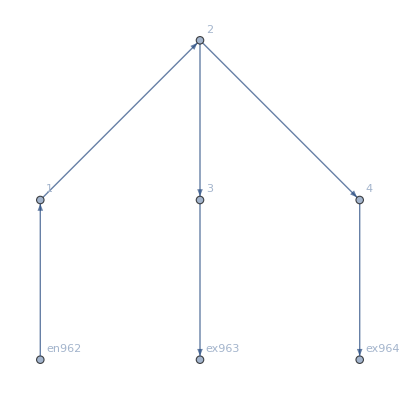

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j965→2.,j967→2.-1. j966,j968→0.+1. j966,j969→2.-1. j966,j970→2.,j971→0.,j972→0.,j973→0.,j974→0.,j975→0.,j976→0.,jt977→0.,jt978→2.,jt980→2.-1. jt979,jt981→0.+1. j966-1. jt979,jt982→0.-1. j966+1. jt979,jt983→0.-1. j966+1. jt979,jt984→0.+1. j966-1. jt979,jt985→0.+1. j966,jt986→0.,jt987→2.-1. j966,jt988→0.,u989→u1000,u992→5.,u993→1.,u994→0.+1. u1000,u995→-2.+1. u1000,u996→0.-1. j966+1. u990,u997→-2.+1. j966+1. u991,u998→5.,u999→1.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```